### 2DOF angular - 3D ambient

-Graphics-

```mathematica
Rspar[ϕ_]:=RotationMatrix[ϕ,{0,0,1}];
Rhinge[ψ_]:=RotationMatrix[ψ,{0,1,0}];
(* Assumption Rcop,x = Subscript[r̂, 1] R in Chen(2016) eq (5). Ixx from "incorporate R" notes.*)
wingsubs={R->Aw/cbar,ycp->R Subscript[r̂, 1],Ixx->(*mwing ycp^2*)0,Izz->cbar^2γ^2mwing};
(*TODO nonlin transmission*)
τinv[ϕo_]:=ϕo /τ1-(ϕo)^3τ2/(3τ1^4);

(*draw*)
drawWing[sol_,a_]:=Module[{pspar,
(*A wing in local fram*)
polyverts={{0,0,0},{0,R,0},{0,R,-cbar},{0,0,-cbar}}
},
pspar=Rspar[ϕ[t]].{0,R,0};
(*Transform to world frame*)
polyverts=(Rspar[ϕ[t]].Rhinge[ψ[t]].polyvertsᵀ)ᵀ;
Graphics3D[{
Thick,
Line[{{0,0,0},pspar}],
Opacity[0.3],
Polygon[polyverts],
Opacity[1],
Blue,
Arrow[{paero,paero+1Faero}]
},PlotRange->{{-20,20},{-20,20},{-10,10}},FaceGrids->All]/.sol/.t->a//.wingsubs/.params
];

plotTrajs[sol_,t2_]:=Module[{t1=t2-Ndt dt/.params,FD=Faero[[1]],
ϕmag=First@FindMaximum[{Abs[ϕ[t]/.sol],t1≤t≤t2},{t,(t1+t2)/2}],
ψmag=First@FindMaximum[{Abs[ψ[t]/.sol],t1≤t≤t2},{t,(t1+t2)/2}],
avglift=NIntegrate[Faero[[3]]/.sol//.wingsubs/.params,{t,t1,t2}]/(t2-t1)*1000/9.81,
σamax=0.35},
Print["ϕmag=",ϕmag,", ψmag=",ψmag,", avglift=",avglift];
{
Plot[τinv[ϕ[t]/.sol]//.wingsubs/.params,{t,t1,t2},PlotLabel->σact,GridLines->{None,{-σamax,σamax}},PlotRange->Full],
Plot[ϕ[t]/.sol,{t,t1,t2},PlotLabel->ϕ,GridLines->{None,{-ϕmag,ϕmag}}],
Plot[ψ[t]/.sol,{t,t1,t2},PlotLabel->ψ,GridLines->{None,{-1.24,-ψmag,ψmag,1.24}}],
Plot[Faero[[3]]*1000/9.81/.sol//.wingsubs/.params,{t,t1,t2},PlotLabel->"FL [mg]",GridLines->{None,{avglift}},Filling->avglift],
Plot[FD*1000/9.81/.sol//.wingsubs/.params,{t,t1,t2},PlotLabel->"FDx [mg]"](*,
Plot[τact/.c2[]/.params,{t,0,tf},PlotLabel->u],*)
}
];

debugComponentsPlot[sol_,t2_]:=Module[{stiff,t1=t2-Ndt dt/.params,M,inertial,Mdiag,inc,ic},
stiff=D[L2,{q}];
M=D[KE,{dq,2}];
inertial=M.ddq;
Mdiag=DiagonalMatrix@Diagonal[M];
inc=Mdiag.ddq;
ic=(M-Mdiag).ddq;

(*Print[inertial//.wingsubs/.params];*)
Join[
Table[
Plot[Evaluate[{
Legended[inertial[[i]],"i"],
Legended[stiff[[i]]+τdamp[[i]],"g"],
Legended[τaero[[i]],"aero"],
Legended[τinp[[i]]/.c2[],"act"],
Legended[τact/.c2[],"actinp"]
}/.sol//.wingsubs/.params],{t,t1,t2},PlotStyle->{Automatic,Automatic,Automatic,Dashed,Dashed},PlotLabel->If[i==1,"stroke","hinge"]]
,{i,2}],
{},
Table[
Plot[Evaluate[{
Legended[inc[[i]],"inc"],
Legended[ic[[i]],"ic"],
Legended[inertial[[i]],"itot"],
Legended[stiff[[i]],"gtot"]
}/.sol//.wingsubs/.params],{t,t1,t2},PlotStyle->{Automatic,Automatic,Dashed,Automatic},PlotLabel->If[i==1,"stroke","hinge"]]
,{i,2}]
]
];

aeroForce[{ϕ_,ψ_,dϕ_,dψ_}]:=Module[{
sparVecB=Rspar[ϕ].{0,1,0},(*vector along wing*)
chordB=Rspar[ϕ].Rhinge[ψ].{0,0,-1},(*wing chord unit vector*)
le,ne,pcopB,rcopnondim,
eD,eL,α,paero,Caero,Faero
},
(*Leading edge velocity direction*)
le=Cross[dϕ{0,0,1},ycp sparVecB];
ne=Sqrt[le.le]+ϵaero;
(*COP: nondim from Chen*)
rcopnondim=0.25+0.25/(1+Exp[5.0*(1.0-4*(π/2-Sqrt[ψ^2])/π)]);
pcopB=(*{0,0,d}+*)ycp sparVecB+rcopnondim chordB;

(*Lift/drag directions*)
eD=-le/ne;
eL={0,0,1};

(*Aero force calculate*)
α=π/2-ψ;
paero=Rspar[ϕ].({0,ycp,0}+Rhinge[ψ].{0,0,-rcopnondim cbar});
Caero={((CDmax+CD0)/2-(CDmax-CD0)/2 Cos[2α]),CLmax Sin[2α]};
(*Subscript[r̂, 2] from Whitney 2010 (2.23). Assumes Rcopx=ycp stays constant - OK.*)
Faero=1/2ρ dϕ^2 cbar R^3 Subscript[r̂, 2]^2 (Caero[[1]]eD+Caero[[2]]eL Sign[-dϕ]);
Return[{paero,Faero}]
];
(*ψ=π/2 - CD0 should remain in drag.
Need to check lift sign. Trying to coincide with 2D sim results https://github.com/avikde/robobee3d/issues/88
i.e. when stroke vel > 0, hinge ang < 0 for lift.
*)
(*aeroForce[{0,-π/4,1,0}][[2]]//.wingsubs/.params//Simplify*)
```

```mathematica
(*Lagrangian setup*)
(*Clear[τinv];*)
q={ϕ[t],ψ[t]};
dq=D[q,t];
ddq=D[dq,t];
(*for analysis*)
pwing=Rspar[ϕ[t]].({0,ycp,0}+Rhinge[ψ[t]].{0,0,-γ cbar});
(*See https://github.com/avikde/robobee3d/pull/105#issue-349667100 for my replacement of Ixx,Izz*)
KE=1/2Ixx ϕ'[t]^2+1/2Izz ψ'[t]^2+1/2mwing D[pwing,t].D[pwing,t]+1/2ma D[τinv[ϕ[t]],t]^2;
PE=(1/2 kψ ψ[t]^2+1/2(ko ycp^2)ϕ[t]^2+1/2ka τinv[ϕ[t]]^2);
L2=KE-PE;
Llhs=(D[D[L2,{dq}],t]-D[L2,{q}])//Simplify;
(*Llhs=First@Solve[And@@Thread[Llhs=={0,0}],{ϕ''[t],ψ''[t]}]//Simplify*)

(*Add non-lagrangian*)
{paero,Faero}=aeroForce[Join[q,dq]];
τaero=Simplify[D[paero,{q}]ᵀ.Faero,Assumptions->{R>0, Subscript[r̂, 1]>0}];
τdamp=-{0,bψ ψ'[t]};
τinp={1,0}D[τinv[ϕ[t]],ϕ[t]]τact;
τrhs=τaero+τdamp+τinp;

(*Simplify may take a little time*)
eoms=Simplify[Thread[Llhs==τrhs]//.wingsubs,Assumptions->{cbar>0,ψ[t]∈Reals,ycp>0}];
```

```mathematica
(*For analysis*)
compareEomTo2D[]:=Module[{eomsanalysis,Mm,hh},
(*eoms for analysis (comparison to 2D). Also comment out the rcopnondim line*)
(*eomsanalysis=Simplify[Thread[Llhs==(*τrhs*){0,0}](*//.wingsubs*)/.{(*τ2->0,*)ϵaero->0},Assumptions->{cbar>0,ψ[t]<0,ϕ'[t]>0,ycp>0}];
(*Get all the terms on the LHS*)
eomsanalysis=Table[eom[[1]]-eom[[-1]],{eom,eomsanalysis}]//Simplify;*)
(*Mm=D[eomsanalysis,{ddq}]//Simplify;
Print["M=",Mm//MatrixForm];*)
Print["M=",(Mm=D[KE,{dq,2}]/.{(*τ2->0,*)ϵaero->0}//Simplify)//MatrixForm];
(*Other terms*)
hh=Llhs-Mm.{ϕ''[t],ψ''[t]}//Simplify;
Print["h=",hh];
Print["N=",D[PE,{q}]/.{(*τ2->0,*)ϵaero->0}//Simplify//MatrixForm];
(*CoefficientList[eomsanalysis[[2]],ϕ''[t]]*)
(*Other EOM stuff to copy into Julia. UNCOMMENT "Clear[τinv];"*)
Print[
Simplify[D[Rspar[ϕ].({0,ycp,0}+Rhinge[ψ].{0,0,-rcopnondim cbar}),{{ϕ,ψ}}]]];
Print[Cross[dϕ{0,0,1},ycp Rspar[ϕ].{0,1,0}]];
];
(*compareEomTo2D[]*)
```

Period=6.075, freq=164.609

ϕmag=0.684568, ψmag=1.12413, avglift=119.132

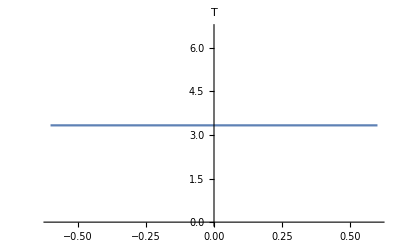
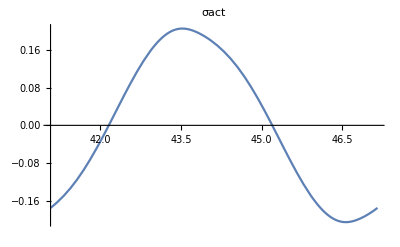
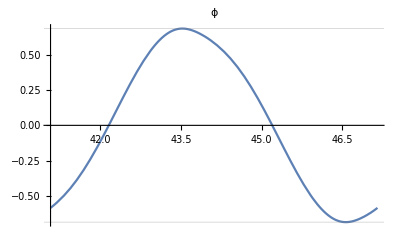
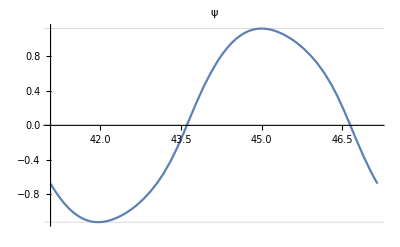
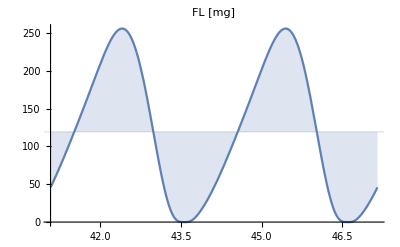
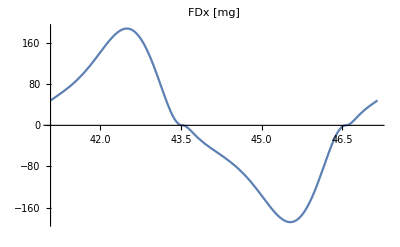
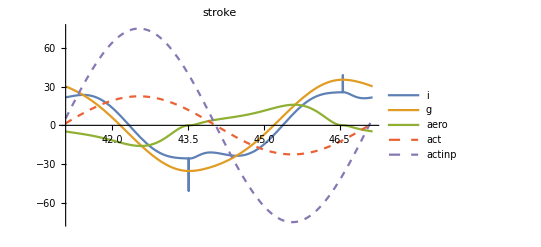
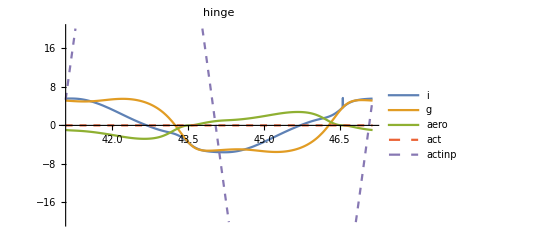

```mathematica
(*wing params r1h,r2h from Chen(2016): see the "incorporate R" notes. N is from the julia traj (just used to map dt).*)
paramsFixed={ko->0.55,ma->6,ka->150,Subscript[r̂, 1]->0.49,Subscript[r̂, 2]->0.551,ϵaero->0.001,CDmax->3.4,CLmax->1.8,CD0->0.4,ρ->1.225*0.001,γ->0.5,Ndt->45};
(*Original robobee*)
paramsOpt=Thread[{cbar,τ1,mwing,kψ,bψ,τ2,Aw,dt}->{
3.2,
3.3333, 
0.52, 
5, 
3,
0, 
54.4, 
0.135
}];
(*paramsOpt=Thread[{cbar,τ1,mwing,kψ,bψ,τ2,Aw,dt}->{
4.928,
(*15.98*)3.3333, 
0.971, 
(*26.653*)16, 
(*19.792*)8,
(*31.959*)(*29*)0, 
97.113, 
(*0.087*)0.145
}];*)
params=Join[paramsFixed,paramsOpt];
eomsp=eoms/.params;
(*other stuff*)
ic3={ϕ[0]==0,ψ[0]==0.01,ϕ'[0]==0.01,ψ'[0]==0};
(*c1={τ->0.08Sin[2π 130t]};*)
Clear[c2];
c2[]:=Module[{freq=1/(Ndt*dt),thCoeff=0.0},(*0.1 for flattened sine used in robobee*)
τact->75((1+thCoeff)Cos[2π freq t]-thCoeff Cos[6π freq t])
];
(*Make sure reasonable*)
eomsfinal=Join[eomsp,ic3]/.c2[]/.params;
(*eomsfinal/.Thread[q->{0.3,0.2}]/.Thread[dq->{0.1,0.1}]*)
(*Sim*)
tf=50;
sol=First@NDSolve[eomsfinal,q,{t,0,tf}];
sol=Join[sol,Thread[dq->D[q/.sol,t]]];
sol=Join[sol,Thread[ddq->D[dq/.sol,t]]];
sols={sol};
Nn=Length@sols;
Print["Period=",Ndt*dt/.params,", freq=",1000/(Ndt*dt/.params)];
t2=tf-2.85;
t1=t2-Ndt*dt/.params;
Join[
{Plot[1/D[τinv[ϕo1],ϕo1]/.ϕo1->ϕo//.wingsubs/.params,{ϕo,-0.6,0.6},PlotLabel->"T"]},
plotTrajs[sol,t2],
debugComponentsPlot[sol,t2],
{
ParametricPlot[Evaluate@Table[Legended[{ϕ[t],ψ[t]}/.sols[[i]],ToString[i]],{i,Nn}],{t,t1,t2},AspectRatio->1,AxesLabel->{ϕ,ψ}],
ParametricPlot[Evaluate@Table[Legended[{ϕ'[t],ψ[t]}/.sols[[i]],ToString[i]],{i,Nn}],{t,t1,t2},AspectRatio->1,AxesLabel->{ϕ',ψ}],
(*Show@Table[
,{soli,{{sols3,sols4,sols5}}}],*)
Animate[drawWing[sols[[1]],a],{a,t1,t2},(*AnimationRepetitions->1,*)DefaultDuration->4]
}
]
```

```mathematica
π/2-α/.Last@Maximize[{(CLmax Sin[2α])/((CDmax+CD0)/2-(CDmax-CD0)/2 Cos[2α])/.params,0≤α≤π/2},α]
```

1.24037

```mathematica
(*Nonlin, sine input, Linear, sine input, flattened lin, flattened nonlin*)
```

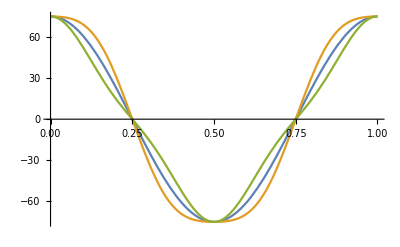

```mathematica
Plot[{75(Cos[2π ϕ]),75(1.1Cos[2π ϕ]-0.1Cos[6π ϕ]),75(0.9Cos[2π ϕ]+0.1Cos[6π ϕ])},{ϕ,0,1}]
```